```mathematica
U0=5.0*10^(-3);
w=1*10^(-6);
Zr=Pi*w^2/(845*10^(-9))*10^(6)*10*0.1
T=50*10^(-6);
W=w*10^(6);
k = 1.380649*10^(-23);
R=8.31446261815324;
mm=1.66053906660*10^(−27);
m=86.909180527;
To=Pi*Sqrt[(2*m*mm*w^2)/(U0*k)];
a1 = 0.652165;
a2=0.0;
a3=0.0;
a4=0.0;
S=5.0;
(*Tend =1.9822137875429475(To*10^6)*10^(-6)/To*)
ko=k*(To/w)^2;
Maxvell=Sqrt[(ko*T)/(mm*m)];
Bolcman=Sqrt[(W^2)*T/(2*U0)]*0.1*10;
translate=1000*w/To (*нм/мкс*);
```

3.71786

```mathematica
p[x1_,x2_,x3_,x4_,t_]:=x1*t+(x2/2)*t^2+(x3/3)*t^3+(x4/4)*t^4;
Tend = Solve[p[a1,a2,a3,a4,t]==S,t][[1,1,2]]
f[t_]:=Piecewise[{
{0,t≤ 0},
{p[a1,a2,a3,a4,t], 0< t≤ Tend},
{f[Tend], t> Tend}
}];
wf[z_]:=W*Sqrt[1+(z/Zr)^2];
U[x_,y_,z_,t_]:=-(U0)*(W/wf[z])^2 * Exp[-2*((x-f[t])^2+y^2)/(wf[z])^2];
(*cycles = 1000;
steps=10;*)
X0 =0.6519;(*-0.020572015959451788;*)
Vx=0.896127;(*0.035746839783390855;*)
Y0=-0.147983;(*-0.07351047069102747;*)
Vy=0.254793;(*-0.028737159861432875;*)
Z0 =-1.25651465;(*-0.41713283543899127;*)
Vz=0.012541;(*-0.02037948842233972;*)
(*Array[P,steps];
Array[Speed,steps];
Array[Unifited,{ steps,steps}];*)
```

7.66677

```mathematica
{xsol,ysol,zsol}=NDSolveValue[
{
(mm*m/(ko)*x''[t])== -D[U[x[t],y[t],z[t],t],x[t]],
(mm*m/(ko)*y''[t])== -D[U[x[t],y[t],z[t],t],y[t]],
(mm*m/(ko)*z''[t])== -D[U[x[t],y[t],z[t],t],z[t]],
x[0]==X0,(*RandomVariate[NormalDistribution[0,Bolcman]],*)
x'[0]==Vx, (*RandomVariate[NormalDistribution[0,Maxvell]],*)
y[0]==Y0,(*RandomVariate[NormalDistribution[0,Bolcman]],*)
y'[0]==Vy, (*RandomVariate[NormalDistribution[0,Maxvell]],*)
z[0]==Z0,(*RandomVariate[NormalDistribution[0,Bolcman]],*)
z'[0]== Vz(*RandomVariate[NormalDistribution[0,Maxvell]]*)
},
(*{
(mm*m/(ko)*x''[t])== -D[U[x[t],t],x[t]],
x[0]==X0(*RandomVariate[NormalDistribution[0,Bolcman]]*),
x'[0]== V0(*RandomVariate[NormalDistribution[0,Maxvell]]*)
},*)
{x,y,z},{t,0,Tend}](*[[1,1,2,0]]*);
ParametricPlot3D[{xsol[t],ysol[t],zsol[t] },{t,0,Tend}]
```

-Graphics3D-

```mathematica
xsol[Tend]
xsol'[Tend]
ysol[Tend]
ysol'[Tend]
zsol[Tend]
zsol'[Tend]
```

4.54881

2.58241

-0.296934

0.822159

0.156125

1.35902

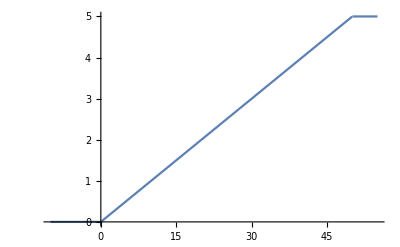

```mathematica
Plot[f[t],{t,-10,Tend*1.1}]
```

```mathematica
-D[U[x,0.5,0.668,0.5],x]
```

-0.0187686 ⅇ^(-1.93745 (0.25+(-0.05+x)^2)) (-0.05+x)

```mathematica
-D[U[x,y,z,0.1],x]*ko/(m*mm) /.x->0.1/.y->0.1 /.z->0.1
```

-6.84375

```mathematica
f[0.1]
```

0.01

```mathematica
U[-0.97,0.83,0.954,0.56]*1000
```

-0.178654

```mathematica
ko/(m*mm)
```

```mathematica
2*10^(-3)/(mm*m/(ko))
```

```mathematica
7.895683520871486
```